### FCM Lib Import

```mathematica
(*Needs["FCMLib`",FileNameJoin[{NotebookDirectory[],"FCMLib-cur.m"}]]*)
Needs["FCMLib`",FileNameJoin[{"../lib","FCMLib-cur.wl"}]]
$FCMLibVersion
```

### Test Operators/Example

#### Example

```mathematica
gspec={
{1,2,1},
{1,3,-1},
{1,4,1},
{2,4,-1},
{3,1,-1},
{3,4,-1},
{3,2,1},
{4,3,1}
};
```

```mathematica
GraphicsRow[{
#,
MatrixForm@Normal@WeightedAdjacencyMatrix@#
},
ImageSize->7×72
]&@FCM[gspec]
```

### Apartheid Example

#### Specification

```mathematica
apthdspec={
{1,2,1},
{1,3,1},
{1,8,1},
{2,3,1},
{3,4,1},
{3,6,-1},
{3,8,1},
{3,9,1},
{4,6,1},
{4,7,1},
{4,9,-1},
{5,2,-1},
{5,3,-1},
{5,6,1},
{5,7,1},
{6,4,1},
{6,7,-1},
{6,8,-1},
{7,5,1},
{7,8,-1},
{8,7,-1},
{9,5,-1},
{9,8,1}
,{2,8,1},
{1,9,1}
};(*last two edges from textbk FCM matrix*)

apthdFCM =FCM[apthdspec,0.14]
apthdG=FCMat[apthdspec];
MatrixForm@apthdG
```

#### Propagation Tests

```mathematica
inp = {1,0,0,0,0,0,0,0,0};
inp.FCMat[apthdspec]
S[inp.FCMat[apthdspec]]
```

```mathematica
inp = {1,0,0,0,0,0,0,0,0};
FCMpass[inp, apthdspec]
FromDigits[%,2]

C1msk = inp;
FCMpass[inp, apthdspec,C1msk]
FromDigits[%,2]

FCMpass[99,apthdspec]
FCMpass[99,apthdspec,C1msk]

FCMRecallSeq[inp,apthdspec]
FromDigits[#,2]&/@%
```

#### Replicate Example

```mathematica
C1msk = {1,0,0,0,0,0,0,0,0};
ex=FCMRecallSeq[inp,apthdspec, C1msk];
Grid@ex
(*FromDigits[#,2]&/@ex*)
```

```mathematica
D1=Last@ex;
D1⟦1⟧=0;
(*D1*)
d1seq = FCMRecallSeq[D1,apthdspec, -C1msk];
Grid@d1seq
```

```mathematica
(*D1*)
d1FreeSeq = FCMRecallSeq[D1,apthdspec,0,0];
Grid@d1FreeSeq
```

```mathematica
FCMView[apthdspec,d1FreeSeq]
```

### Taber’s Platelet Aggregation Example

#### Specification

```mathematica
clotspec={
{1,1,1},
{1,2,0.4},
{1,3,1}, (* edge mising from adj mat in paper *)
{1,4,1},
{2,3,0.5},
{2,6,0.45},
{3,2,0.4},
{3,4,0.75},
{3,6,0.4},
{4,6,0.4},
{5,6,0.45},
{6,2,0.7},
{7,5,-0.6},
{8,6,0.95},
{9,10,-0.9},
{10,6,1},
{11,8,0.95},
{12,11,-0.6}
};(* from Taber et al on quantization effects in FCMs *)

clotverts={
{1,"HCP","Hypercoagulation Positional Factors"},
{2,"stas", "Blood Stasis"},
{3,"inju", "Endothelial Injury"},
{4,"HCF", "Hypercoagulation Factors"},
{5,"ADP","ADP"},
{6,"PAgg", "Platelet Aggregation"},
{7,"clop", "Clopidogrel Ticlopidogrel"},
{8,"A2", "Thromboxane A2"},
{9,"war","Warfarin"},
{10,"K", "Vitamin K Activated Clotting Factors"},
{11,"cox", "Cyclooxidase COX-1"},
{12,"aspi", "Aspirin"}
};
```

```mathematica
clotFCM =FCM[clotverts,clotspec,0.9]
```

```mathematica
Graph[
clotFCM,
GraphLayout->"StarEmbedding"
]
clotG=FCMat[clotFCM];
MatrixForm@clotG
```

#### Run

```mathematica
(*FCMpass[inp_Integer,spec_:MatrixQ,on_Integer:0,off_Integer:0]*)
inp = RandomInteger[{0,1}, 12];
mask = RandomInteger[{-1,1}, 12];

pass=FCMpass[
inp,
clotspec,
mask
];

Grid@{
inp,
mask,
pass
}
```

```mathematica
inp = IntegerDigits[2^9,2,12];
mask = inp;

pass=FCMpass[
inp,
clotspec,
mask
];

Grid@{
inp,
mask,
pass
}
```

```mathematica
FCMRecallSeq[inp,clotspec, mask]//Grid
```

#### Graph Join Dev

```mathematica
nds = {
{1,"HCP","Hypercoagulation Positional Factors"},
{2,"stas", "Blood Stasis"},
{3,"inju", "Endothelial Injury"},
{4,"HCF", "Hypercoagulation Factors"}
};
gspec={{1,2,1},{1,3,-1},{1,4,1},{2,4,-1},{3,1,-1},{3,4,-1},{3,2,1},{4,3,1}};

altGspec={{1,2,1},{1,4,1},{2,4,1},{3,1,-1},{3,2,1},{4,3,1}};
```

```mathematica
(GraphicsRow[{FCMat[#]//MatrixForm,#},Spacings->0])&/@(FCM[nds,#,0.5]&/@{gspec,altGspec})

{MatrixForm@FCMat@#,#}&@FCMJoin[nds,(FCM[nds,#,0.5]&/@{gspec,altGspec}),{1/3,2/3}]
```

```mathematica
GraphicsColumn@{MatrixForm@FCMat@#,#}&@FCMJoin[
clotverts,
(FCM[clotverts,#,0.5]&/@{clotspec,gspec,altGspec}),
{6/10,1/5,1/5},
0.8
]
```

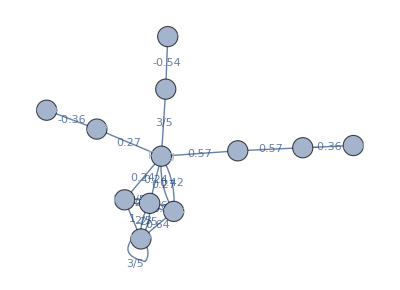

### PSOT v0

```mathematica
psotegsv0={
(* Original Tree structure *)
{1,6,strongOrLink},{2,6,strongOrLink},{3,6,strongOrLink},{4,6,orLink},{5,6,orLink},{30,6,weakOrLink},{31,6,weakOrLink},{32,6,weakOrLink},

{7,10,strongOrLink},{8,10,weakOrLink},{9,10,orLink},{24,10,strongOrLink},

{10,13,strongOrLink},{11,13,strongOrLink},{12,13,weakOrLink},

{14,18,strongOrLink (*unsure*)},{15,18,weakOrLink},{16,18,orLink},{17,18,orLink},

{19,23,strongOrLink (*unsure*)},{20,23,strongOrLink (*unsure*)},{21,23,-strongOrLink},{22,23,-strongOrLink},


(* Loose bits in orig factor tree *)
{25,11,orLink+0.1},(*fudge low fan-in nodes else never triggers*)
{24,7,strongOrLink+0.3},{24,11,strongOrLink},
{23,19,strongOrLink (*unsure*)},{23,20,strongOrLink (*unsure*)},{18,14,strongOrLink (*unsure*)},(*return links for uncertain causation*)


{6,50,andLink},{13,50,andLink},{18,50,andLink},{23,50,andLink} (*,TLD 'and' links*)
(*{50,50,orLink×orLink}, (* weak PSOT self-excitations for temporal correlation(?) *)*)


(*(* see pg 23 in PD+AOM2013 for next set of xlinks *)
{29,13,orLink},{29,21,-orLink},(* s/f links: Effects of successes ,{29,18,orLink} *)
{26,6,-orLink},{26,13,-orLink},(* Effects of Misbehaving grps {26,18,-orLink}, *)

{6,13,weakOrLink},{13,18,weakOrLink},{13,18,weakOrLink},{18,23, weakOrLink},(*rem l->r dep weak links*)
{6,29,weakOrLink} (* eff -> success *)*)
};

psotFCMv0 =FCM[psotvs,psotegsv0,0.7];
```

```mathematica
Graph[psotFCMv0,
GraphLayout->"RadialEmbedding",
ImageSize->72×12
]
```

### Moot

```mathematica
gspec
altGspec
tmpspec=Union[gspec, altGspec]
tstspec=(FCMJoin[{gspec, altGspec}])

GraphicsColumn[
(GraphicsRow[{FCMat[#]//MatrixForm,FCM[#,0.5]},Spacings->0])&/@{gspec,altGspec,tmpspec,tstspec},
Spacings->0, ImageSize->Large
]
```

```mathematica
(*Table[Flatten@{List@@e,PropertyValue[{gg, e}, EdgeWeight]},{e, EdgeList@gg}]*)
Table[{e,PropertyValue[{gg, e}, EdgeWeight]},{e, EdgeList@gg}]
Table[{e,PropertyValue[{altG, e}, EdgeWeight]},{e, EdgeList@altG}]
%~Join~%%
GroupBy[%, First->Last]
Table[{v,PropertyValue[{altG, v}, VertexLabels]},{v, VertexList@#}]&/@{gg,altG}
```

#### Test Random/Async Evolution Operator

```mathematica
({1,0,0,0}⟦{2,3}⟧)
(FCMat[gspec]⟦;;,;;⟧)//MatrixForm
(FCMat[gspec]⟦;;,{2,3}⟧)//MatrixForm
```

```mathematica
FCMpass[{1,0,0,0},gspec]
FCMAsyncPass[{1,0,0,0},gspec,3,{0,0,0,0}]
FCMAsyncPass[{1,0,0,0},gspec,3,0]
FCMAsyncPass[{1,0,0,0},gspec,3,0,0]
FCMAsyncPass[8,gspec,3,{0,0,0,0}]
IntegerDigits[%,2,4]

FCMAsyncRecallSeq[{1,0,0,0},gspec,1, {0,1,0,1}]
```